Fitting a gaussian to the spin orbit coupling part of the Woods-Saxon potential
Start by defining global constants

```mathematica
DIFFUSIVITY=0.6;
R0 = 1.2; (*[fm]*)
Ac = 10; (*number of core nucleons*)
J = 0.5; (*total angular momentum*)
l = 1;  (*orbital angular momentum*)
VLS = -21; (*[MeV]*)
rEps = 1.*^-4;(*small r parameter*)

rUpperVals = Subdivide[0.7, 15, 10000];
rForcingVals = Subdivide[0, 0.69, 100] ;
rVals = Join[rForcingVals,rUpperVals];
V0 = (-11.39)*(-1)^l - 51.13;
Rcore = R0*Ac^(1/3);
spinCouplingTerm = ((J*(J + 1))/2) - ((l*(l + 1))/2) - 0.375;
```

```mathematica
(*generate the geometric betas for use in our gaussians
NOTE: the success of this method is VERY dependent on the initial values of r1 and a!! good choices seem to be a=1.4ish for l=0, and a=1.3ish for l=1. i figure this out by finding the maximum difference between our estimated gaussian potential and the real woods-saxon later (once the curve fit has been done), and choosing an a which makes this small. there is Absolutely a better more numeric way to pick a but this works for now so i'm sticking with it
*)
generateBetas[numGaussians_Integer, rStart_: 0.3, rEnd_: 3.2] := Module[
{a, rn},
a = (rEnd/rStart)^(1/(numGaussians - 1));
rn = Table[rStart*a^i, {i, 0, numGaussians - 1}];
  1/(rn^2)
];
generateBetas[12]
```

{11.1111,7.22509,4.69817,3.05502,1.98655,1.29177,0.839985,0.546207,0.355175,0.230956,0.150181,0.0976562}

We now define our Woods-Saxon potential and its derivative for use in the spin orbit fitting

```mathematica
FWS[r_] := 1/(1+E^((r-Rcore)/DIFFUSIVITY))
dFWS[r_] := FullSimplify[FWS'[r]]
dFWS[r]
```

-(123.927 ⅇ^(1.66667 r))/((74.3564+ⅇ^(1.66667 r))^2)

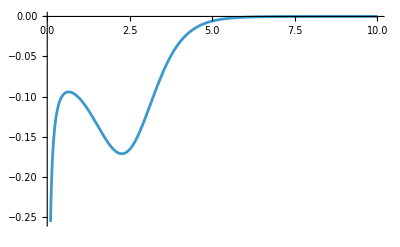

```mathematica
spinorbitfittingfunction[r_] := 1/r dFWS[r]
lowrForcingFunction[r_]:= 2r(r-1.37351428571)
Plot[spinorbitfittingfunction[r],{r,0.1,10}]
```

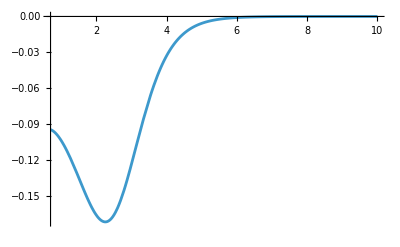

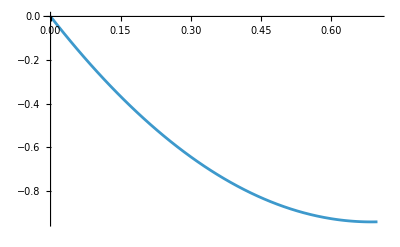

-Graphics-

```mathematica
p1=Plot[spinorbitfittingfunction[r],{r,0.7,10}]
p2=Plot[lowrForcingFunction[r],{r,0,0.7}]
Show[p1, p2]
```

```mathematica
SpinOrbitEvaluatedrVals = spinorbitfittingfunction[rUpperVals];
ForcingEvaluatedrVals = lowrForcingFunction[rForcingVals];
FullEvaluatedrVals = Join[ForcingEvaluatedrVals, SpinOrbitEvaluatedrVals];
betas12 = generateBetas[12];(*add the design matrix which represents the least squares problem (without any ridge regression yet!*)
designMatrix[rList_, betas_] := 
  Transpose[Table[2  betas[[i]] Exp[-betas[[i]]*rList^2], {i, Length[betas]}]];

modifiedrVals = Subdivide[0.1, 1, 9];
designMatrix[rUpperVals, betas12];

(*do the curvefit using ridge regression, adding column scaling*)
ridgeSolve[designMatrix_,targetVector_,lambda_:1.*^-6]:=Module[
{X=designMatrix,y=targetVector,numSamples,numFeatures,columnNorms,Xscaled,identityMat,normalMatrix,rhs,scaledCoeffs,coeffs}(*renaming things so i don't have to type all these words every time
designMatrix (x) is our matrix of gaussians which we wanna converge towards our WS
targetVector (y) is what we wanna fit to (in this case our analytic WS)
lambda is related to the penalty term for having weirdly large coefficients - i picked small numbers for this and it seemed to work ok
numSamples is the number of r values
numFeatures is the numer of parameters to be curve fitted
*),

{numSamples,numFeatures}=Dimensions[X];

(*do column scaling - find norm of each column*)columnNorms=Table[If[Norm[X[[All,j]]]==0,1.,Norm[X[[All,j]]]],{j,numFeatures}];
(*normalise columns so each has norm=1*)
Xscaled=Transpose[Transpose[X]/columnNorms];

(*do the curvefit with the ridge regression term added*)
identityMat=IdentityMatrix[numFeatures];
normalMatrix=Transpose[Xscaled].Xscaled;
rhs=Transpose[Xscaled].y;(*mathematica LinearSolve solves linear system of equations generated by our regression equation*)
scaledCoeffs=LinearSolve[normalMatrix+lambda*identityMat,rhs];(*divide coefficients by the norm of each column to undo the column scaling we did earlier and get the true params!*)
coeffs=scaledCoeffs/columnNorms;
coeffs
];

(*do the curve fit to the woods-saxon without any spin orbit term added*)
design12 = designMatrix[rVals, betas12];

coeffs12 = ridgeSolve[design12, FullEvaluatedrVals, 1.*^-6];
Print[coeffs12];

(*put them V0s back in to get the gaussians yippee!*)
fittedTwelveBasic = V0*(design12 . coeffs12);
```

10102

12

{10102,12}

{10102}

{-0.460384,2.51557,-4.50942,3.12398,-0.00178223,-2.00406,1.32756,-0.0817432,1.74693,-2.178,-0.783073,0.18386}

```mathematica
analytic12GaussFull =designMatrix[rVals,betas12].coeffs12;
```

```mathematica
safeLog[list_] := Map[If[# < 0, Log[-#], Indeterminate] &, list];

p1 = ListLinePlot[{Transpose[{rVals, FullEvaluatedrVals}](*, 
    Transpose[{rVals, analytic12GaussFull}]*)},
   PlotLegends -> {"Analytic WS (no SO)"(*, "2-Gauss Fit"*)},
   PlotRange -> All, AxesLabel -> {"r (fm)", "V(r) (MeV)"}];

p2 = ListLinePlot[{Transpose[{rVals, safeLog[FullEvaluatedrVals]}], 
    Transpose[{rVals, safeLog[analytic12GaussFull]}]},
   PlotLegends -> {"ln(-Analytic WS)", "ln(-2-Gauss Fit)"},
   PlotRange -> All, AxesLabel -> {"r (fm)", "ln(-V)"}];

GraphicsGrid[{{p1}, {p2}}]
```

-Graphics-